#### Docked cell

```mathematica
CurrentValue[EvaluationNotebook[],DockedCells]={
Cell[BoxData[ToBoxes[DynamicModule[{time=0,paclet="",url=None},Grid[{
{
Button["Reload paclet",
Needs["PacletTools`"];
time=First@AbsoluteTiming[
Module[{pacletDirectory},
Unprotect["Wolfram`Multicomputation`*","Wolfram`Multicomputation`**`*"];
ClearAll["Wolfram`Multicomputation`*","Wolfram`Multicomputation`**`*"];
PacletUninstall[PacletFind["*Multicomputation*"]];
pacletDirectory=ExpandFileName@FileNameJoin[{NotebookDirectory[],"..","Multicomputation"}];
Scan[If[DirectoryQ[#],DeleteDirectory[#,DeleteContents->True],DeleteFile[#]]&,FileNames@FileNameJoin[{pacletDirectory,"build","*"}]];
(*paclet=PacletTools`PacletBuild[pacletDirectory,OverwriteTarget->True]*)paclet=CreatePacletArchive[pacletDirectory];
If[!FailureQ[paclet],
(*paclet=paclet["PacletArchive"];*)
PacletInstall[paclet,ForceVersionInstall->True];
<<Wolfram`Multicomputation`;Needs["Wolfram`Multicomputation`"->"MC`"]]
]
];
],
Dynamic[Column@{ClickToCopy[FileNameTake[paclet],CloudObject[paclet,Permissions->"Public"]],Quantity[time,"Seconds"]}]
},
{Button["Upload paclet",
CloudObject`Private`$allowInternetCheck=True;
DeleteFile[CloudObject["Multicomputation.paclet"]];
url=URLShorten@CopyFile[File[paclet],CloudObject["Multicomputation.paclet",Permissions->"Public"]]
],
Dynamic[ClickToCopy@url],
Dynamic[$CloudUserID]

}
},Alignment->Left]]]]
]
};
```

### Kinds of Multiway systems

#### States

Global:
- Expression
- Hypergraph
- String
- Turing/CA/etc. state

Local (destroyable pieces of a global state):
- Subexpressions
- Subset of hyperedges
- Substrings

Token (local state + coordinate):
- Hyperedge (intrinsic coordinate)
- Subexpression + tree position
- Character + string position

#### Events

Input:
- Global state
-

Local non-branching (single state position, single output)

#### Global state, local non-branching event

## Playground

```mathematica
multi=HypergraphMulti[x·y,{x_·(y_·z_):>(x·y)·z,(x_·y_)·z_:>x·(y·z),a_·e:>a,a_:>a·e,a_·inv[a_]:>e,e:>a_·inv[a_]}]
```

Multi[…]

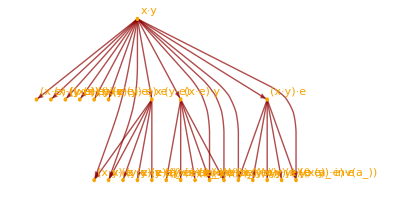

```mathematica
multi["CausalGraph",2,"Expression",AspectRatio->1/2]
```

```mathematica
multi=HypergraphMulti["BB",{"BB"->"AB","A"->"BA"}]
```

Multi[…]

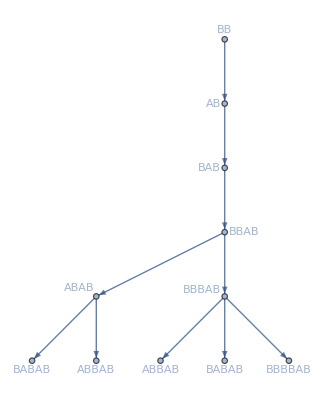

```mathematica
multi["Graph",5,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->v_:>FromLinkedHypergraph[v,"String"]]
```

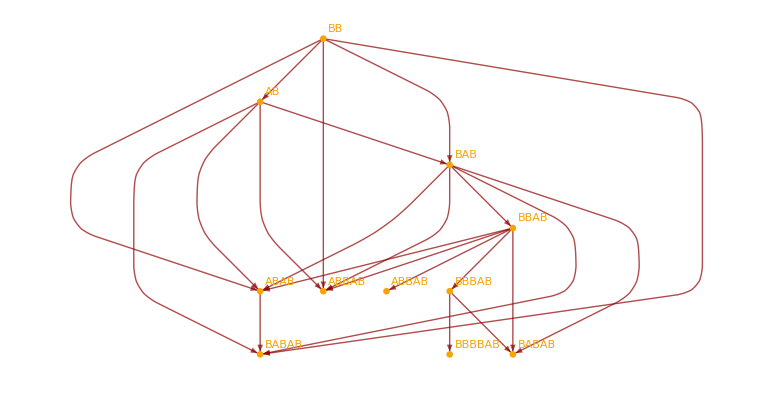

```mathematica
cg=multi["CausalGraph",5,"String"]
```